```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
f[x_,r_]:=(1/5)+(7/10)*(1/(1+Exp[80*(1-x)]))-r*x^4
f1[x_]=(1/5)+(7/10)*(1/(1+Exp[80*(1-x)]))
f2[x_,r_] = r*x^4

Manipulate[Show[Plot[{f1[x],f2[x,r]},{x,-2,2},
PlotRange->{Full,{0,1}}],
ListPlot[{x,f2[x,r]}/.NSolve[f2[x,r]==f1[x],x,Reals],
 PlotStyle-> Red]], {r,0,1}]
```

1/5+7/(10 (1+ⅇ^(80 (1-x))))

r x^4

```mathematica
(□_□)_□
```

(□_□)_□

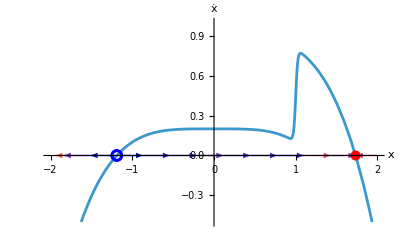

First::nofirst: {} has zero length and no first element.

First[{}]

```mathematica
(*rc =0.261*)
r = 0.1;
sol[rvar_] := NSolve[f[x,rvar]==0, x,Reals];
p1 = Plot[f[x,r], {x, -2, 2}, PlotRange->{Full, {-0.5, 1}}, AxesLabel->{"x", OverDot["x"]}];
p2= StreamPlot[{f[x,r], 0}, {x, -2, 2}, {y, -0.1, 0.1}];
p3= ListPlot[{{x/.sol[r][[2]], 0}}, PlotMarkers->{Graphics[{Red, Disk[]}], 10}];
p4= ListPlot[{{x/.sol[r][[1]], 0}}, PlotMarkers->{Graphics[{Blue, Circle[]}], 10}];
Show[p1, p2, p3, p4]
```

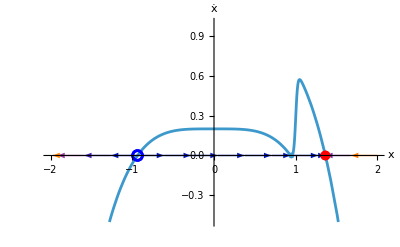

```mathematica
r = 0.261;
sol[rvar_] := NSolve[f[x,rvar]==0, x,Reals];
p1 = Plot[f[x,r], {x, -2, 2}, PlotRange->{Full, {-0.5, 1}}, AxesLabel->{"x", OverDot["x"]}];
p2= StreamPlot[{f[x,r], 0}, {x, -2, 2}, {y, -0.1, 0.1}];
p3= ListPlot[{{x/.sol[r][[1]], 0}}, PlotMarkers->{Graphics[{Blue, Circle[]}], 10}];
p4= ListPlot[{{x/.sol[r][[2]], 0}}, PlotMarkers->{Graphics[{Red, Disk[{0, 0}, 1, {Pi/2, 3 Pi/2}], Red, Circle[{0, 0}, 1, {Pi/2, 3 Pi / 2}], Blue, Circle[{0, 0}, 1, {-Pi/2, Pi/2}]}], 10}];
p5= ListPlot[{{x/.sol[r][[4]], 0}}, PlotMarkers->{Graphics[{Red, Disk[]}], 10}];
Show[p1, p2, p3, p4,p5]
```

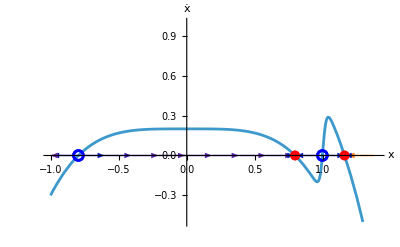

```mathematica
r = 0.5;
sol[rvar_] := NSolve[f[x,rvar]==0, x,Reals];
p1 = Plot[f[x,r], {x, -1,1.4}, PlotRange->{Full, {-0.5, 1}}, AxesLabel->{"x", OverDot["x"]}];
p2= StreamPlot[{f[x,r], 0}, {x, -1, 1.4}, {y, -0.05, 0.05}];
p3= ListPlot[{{x/.sol[r][[1]], 0}}, PlotMarkers->{Graphics[{Blue, Circle[]}], 10}];
p4= ListPlot[{{x/.sol[r][[2]], 0}}, PlotMarkers->{Graphics[{Red, Disk[]}], 10}];
p5= ListPlot[{{x/.sol[r][[3]], 0}}, PlotMarkers->{Graphics[{Blue, Circle[]}], 10}];
p6= ListPlot[{{x/.sol[r][[4]], 0}}, PlotMarkers->{Graphics[{Red, Disk[]}], 10}];
Show[p1, p2, p3, p4,p5,p6]
```

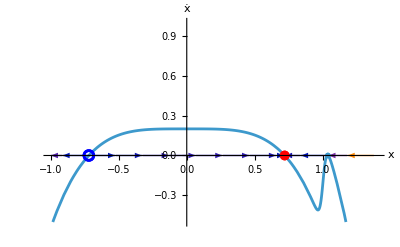

```mathematica
(*This is r_c since it is the largest r that causes a change in the number of fixed points. For r > 0.749, we will always have 2 fixed points. Moreover, for r > 0.749 the temperature will always decrease indicating that the dynamics bifurcates to a snowball earth. *)
r = 0.749;
sol[rvar_] := NSolve[f[x,rvar]==0, x,Reals];
p1 = Plot[f[x,r], {x, -1, 1.4}, PlotRange->{Full, {-0.5, 1}}, AxesLabel->{"x", OverDot["x"]}];
p2= StreamPlot[{f[x,r], 0}, {x, -1, 1.4}, {y, -0.05, 0.05}];
p3= ListPlot[{{x/.sol[r][[1]], 0}}, PlotMarkers->{Graphics[{Blue, Circle[]}], 10}];
p4= ListPlot[{{x/.sol[r][[2]], 0}}, PlotMarkers->{Graphics[{Red, Disk[]}], 10}];
p5= ListPlot[{{x/.sol[r][[4]], 0}}, PlotMarkers->{Graphics[{Red, Disk[{0, 0}, 1, {-Pi/2, Pi/2}], Blue, Circle[{0, 0}, 1, {Pi/2, 3 Pi / 2}], Red, Circle[{0, 0}, 1, {-Pi/2, Pi/2}]}], 10}];
Show[p1, p2, p3, p4,p5]
```

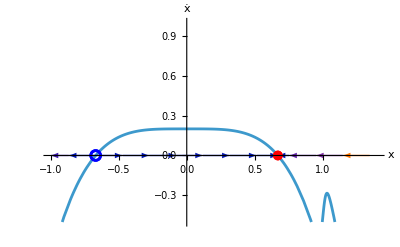

```mathematica
(*Not necessary to keep.*)
r = 1;
sol[rvar_] := NSolve[f[x,rvar]==0, x,Reals];
p1 = Plot[f[x,r], {x, -1, 1.4}, PlotRange->{Full, {-0.5, 1}}, AxesLabel->{"x", OverDot["x"]}];
p2= StreamPlot[{f[x,r], 0}, {x, -1, 1.4}, {y, -0.05, 0.05}];
p3= ListPlot[{{x/.sol[r][[1]], 0}}, PlotMarkers->{Graphics[{Blue, Circle[]}], 10}];
p4= ListPlot[{{x/.sol[r][[2]], 0}}, PlotMarkers->{Graphics[{Red, Disk[]}], 10}];

Show[p1, p2, p3, p4]
```

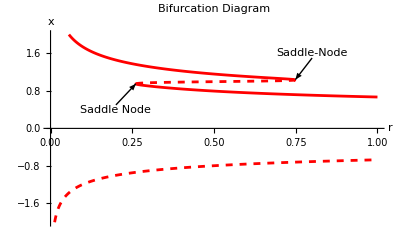

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
f[x_,r_]:=(1/5)+(7/10)*(1/(1+Exp[80*(1-x)]))-r*x^4

(*Range for r values*)
rValues=N[Range[0,1,1/1000]];

interval1Points={}; (*(-∞,0)*)
interval2Points={}; (*(0,0.95)*)
interval3Points={}; (*(0.95,1.04)*)
interval4Points={}; (*(1.04,∞)*)

Do[solutions=NSolve[f[x,r]==0,x,Reals];
Do[point={r,x}/. solution;
If[point[[2]]<0,AppendTo[interval1Points,point],
If[0<=point[[2]]<0.95,AppendTo[interval2Points,point],
If[0.95<point[[2]]<1.04,AppendTo[interval3Points,point],
(*"Else""*)AppendTo[interval4Points,point]]]],{solution,solutions}],{r,rValues}];


Show[
ListPlot[interval1Points,PlotRange->{{0,1},{-2,2}},PlotStyle->{Red,Dashed},Joined->True],
ListPlot[interval2Points,PlotRange->{{0,1},{-2,2}},PlotStyle->{Red},Joined->True],ListPlot[interval3Points,PlotRange->{{0,1},{-2,2}},PlotStyle->{Red,Dashed},Joined->True],
ListPlot[interval4Points,PlotRange->{{0,1},{-2,2}},PlotStyle->{Red},Joined->True],
Graphics[{
{Black,Arrow[{{0.8,1.5},{0.749,1.04}}],Text[Style["Saddle-Node",Black],{0.8,1.6}]},{Black,Arrow[{{0.2,0.5},{0.261,0.95}}],Text[Style["Saddle Node",Black],{0.2,0.4}]}
}],
AxesLabel->{"r","x"},PlotLabel->"Bifurcation Diagram"
]
```